(* Markdown metadata *)
<|
"Date":>Now,
"ExportOptions"→{
(*"UseImageInput"→True*)
}
|>

VQM SYMBOL

## QArgColorPlot

```mathematica
QArgColorPlot[fun, {x, xmi, xma}, opt]
```

is used like the usual Plot command. It gives a two-dimensional plot of a complex-valued function f of a single real variable x in the range {x0,x1}.
The plot shows the curve Abs[f] with area between the curve and the x-axis colored by Hue[Arg[f[x]]/(2 Pi)].
The default options of Plot are changed to Axes->{True,None}, Frame->True. Package: VQM`ArgColorPlot`

### Details

QArgColorPlot has 1 call pattern

QArgColorPlot has the following Options

ClippingStyle

None

ColorFunction

Automatic

ColorFunctionScaling

True

Compiled

True

DataRange

Automatic

Filling

None

FillingStyle

Automatic

InterpolationOrder

None

Joined

True

LabelingFunction

Automatic

LabelingSize

Automatic

MaxPlotPoints

Infinity

Mesh

None

MeshFunctions

{#1 & }

MeshShading

None

MeshStyle

Automatic

Opacity

1

PlotLabels

None

PlotLayout

"Overlaid"

PlotLegends

None

PlotMarkers

None

PlotStyle

Automatic

QBottomLine

0

QBrightness

1

QPlotDown

False

QSaturation

1

QShiftPlot

0

QSquared

False

ScalingFunctions

None

TargetUnits

Automatic

PerformanceGoal

$PerformanceGoal

PlotTheme

$PlotTheme

QArgColorPlot can take Options from the following

ClippingStyle -> None

ColorFunction -> Automatic

ColorFunctionScaling -> True

Compiled -> True

DataRange -> Automatic

Filling -> None

FillingStyle -> Automatic

InterpolationOrder -> None

Joined -> True

LabelingFunction -> Automatic

LabelingSize -> Automatic

MaxPlotPoints -> Infinity

Mesh -> None

MeshFunctions -> {#1 & }

MeshShading -> None

MeshStyle -> Automatic

Opacity -> 1

PlotLabels -> None

PlotLayout -> "Overlaid"

PlotLegends -> None

PlotMarkers -> None

PlotStyle -> Automatic

QBottomLine -> 0

QBrightness -> 1

QPlotDown -> False

QSaturation -> 1

QShiftPlot -> 0

QSquared -> False

ScalingFunctions -> None

TargetUnits -> Automatic

PerformanceGoal :> $PerformanceGoal

PlotTheme :> $PlotTheme

QArgColorPlot has the following Attributes

HoldAll

Protected

### Examples

#### Basic Examples

Load the package:

```mathematica
Needs["VQM`ArgColorPlot`"]
```

Basic usage

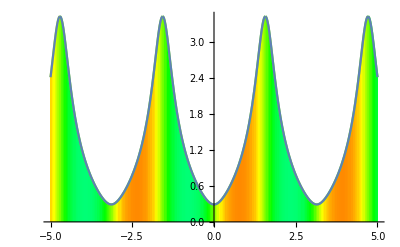

```mathematica
QArgColorPlot[Tan[x + 0.3 I], {x,-5,5}]
```

#### Options

##### ClippingStyle

Possible option values for ClippingStyle include:

```mathematica
QArgColorPlot[ClippingStyle -> None]
```

##### ColorFunction

Possible option values for ColorFunction include:

```mathematica
QArgColorPlot[ColorFunction -> Automatic]
```

##### ColorFunctionScaling

Possible option values for ColorFunctionScaling include:

```mathematica
QArgColorPlot[ColorFunctionScaling -> True]
```

##### Compiled

Possible option values for Compiled include:

```mathematica
QArgColorPlot[Compiled -> True]
```

##### DataRange

Possible option values for DataRange include:

```mathematica
QArgColorPlot[DataRange -> Automatic]
```

##### Filling

Possible option values for Filling include:

```mathematica
QArgColorPlot[Filling -> None]
```

##### FillingStyle

Possible option values for FillingStyle include:

```mathematica
QArgColorPlot[FillingStyle -> Automatic]
```

##### InterpolationOrder

Possible option values for InterpolationOrder include:

```mathematica
QArgColorPlot[InterpolationOrder -> None]
```

##### Joined

Possible option values for Joined include:

```mathematica
QArgColorPlot[Joined -> True]
```

##### LabelingFunction

Possible option values for LabelingFunction include:

```mathematica
QArgColorPlot[LabelingFunction -> Automatic]
```

##### LabelingSize

Possible option values for LabelingSize include:

```mathematica
QArgColorPlot[LabelingSize -> Automatic]
```

##### MaxPlotPoints

Possible option values for MaxPlotPoints include:

```mathematica
QArgColorPlot[MaxPlotPoints -> Infinity]
```

##### Mesh

Possible option values for Mesh include:

```mathematica
QArgColorPlot[Mesh -> None]
```

##### MeshFunctions

Possible option values for MeshFunctions include:

```mathematica
QArgColorPlot[MeshFunctions -> {#1 & }]
```

##### MeshShading

Possible option values for MeshShading include:

```mathematica
QArgColorPlot[MeshShading -> None]
```

##### MeshStyle

Possible option values for MeshStyle include:

```mathematica
QArgColorPlot[MeshStyle -> Automatic]
```

##### Opacity

Possible option values for Opacity include:

```mathematica
QArgColorPlot[Opacity -> 1]
```

##### PlotLabels

Possible option values for PlotLabels include:

```mathematica
QArgColorPlot[PlotLabels -> None]
```

##### PlotLayout

Possible option values for PlotLayout include:

```mathematica
QArgColorPlot[PlotLayout -> "Overlaid"]
```

##### PlotLegends

Possible option values for PlotLegends include:

```mathematica
QArgColorPlot[PlotLegends -> None]
```

##### PlotMarkers

Possible option values for PlotMarkers include:

```mathematica
QArgColorPlot[PlotMarkers -> None]
```

##### PlotStyle

Possible option values for PlotStyle include:

```mathematica
QArgColorPlot[PlotStyle -> Automatic]
```

##### QBottomLine

Possible option values for QBottomLine include:

```mathematica
QArgColorPlot[QBottomLine -> 0]
```

##### QBrightness

Possible option values for QBrightness include:

```mathematica
QArgColorPlot[QBrightness -> 1]
```

##### QPlotDown

Possible option values for QPlotDown include:

```mathematica
QArgColorPlot[QPlotDown -> False]
```

##### QSaturation

Possible option values for QSaturation include:

```mathematica
QArgColorPlot[QSaturation -> 1]
```

##### QShiftPlot

Possible option values for QShiftPlot include:

```mathematica
QArgColorPlot[QShiftPlot -> 0]
```

##### QSquared

Possible option values for QSquared include:

```mathematica
QArgColorPlot[QSquared -> False]
```

##### ScalingFunctions

Possible option values for ScalingFunctions include:

```mathematica
QArgColorPlot[ScalingFunctions -> None]
```

##### TargetUnits

Possible option values for TargetUnits include:

```mathematica
QArgColorPlot[TargetUnits -> Automatic]
```

##### PerformanceGoal

Possible option values for PerformanceGoal include:

```mathematica
QArgColorPlot[PerformanceGoal :> $PerformanceGoal]
```

##### PlotTheme

Possible option values for PlotTheme include:

```mathematica
QArgColorPlot[PlotTheme :> $PlotTheme]
```

#### Definitions

Examine all definitions:

```mathematica
GeneralUtilities`PrintDefinitionsLocal[QArgColorPlot]
```

### See Also

QBottomLine | QBrightness | QCombinedPlot | QCurveStyle | QHorizontalRange | QListArgColorPlot | QListCombinedPlot | QListSpinorCombinedPlot | QListSpinorPlot | QNiceTicks | QPlotDown | QSaturation | QShiftPlot | QSpinorCombinedPlot | QSpinorPlot | QSquared

### Related Guides

Guide 1

Guide 2

### Related Links

Link 1

Link 2

Made with SimpleDocs